```mathematica
simulateQuarkYukawaBulk[ptclLabel_,nTrials_]:=Module[{yu,yd,myu,myd,output={}},
Do[
{yu,yd}=quarkData[[i]];
myu=Minors[yu];myd=Minors[yd];
AppendTo[output,QuarkEffYukawa[yu,yd,myu,myd][ptclLabel]],{i,nTrials}
];
output
]
```

```mathematica
Length[quarkData]
```

1321

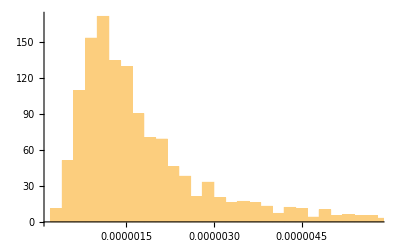

```mathematica
Histogram[simulateQuarkYukawaBulk["u",Length[quarkData]]]
```

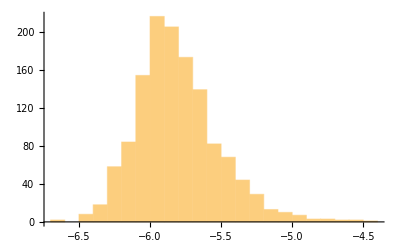

```mathematica
Histogram[Log10[simulateQuarkYukawaBulk["u",Length[quarkData]]]]
```

```mathematica
With[
{min = -1/2; max = 2};
Show[
ContourPlot[FermionProfileBulkOverlap[cL,cR],
{cL,min-0.1,max+0.1},{cR,min-0.1,max+0.1},
Contours->{
10^-1,10^-2,10^-4
},
ContourStyle->{Thick,#2},
ContourShading->None,
PlotPoints->100
]
]
```